# 九州大学理学部数学科3年 1SC16340S 都田悠輔 「情報数学・同演習」課題

## 3. Mathematica で線形代数

2018年6月13日

## 練習問題

### 問題1.

5Ω, 2Ω, 15Ω, 6Ω, 100Ω の抵抗が下図のように接続されていて, 
それぞれの抵抗を流れる電流を I_1,I_2,I_3,I_4,I_5 とする. 
但し, I_1,I_2,I_3,I_4 は左から右,I_5 は下から上に流れる電流値とする. 
回路の左から右に 2 A の直流電流が流れているとき, I_1,I_2,I_3,I_4,I_5 の値を求めよ.
-Graphics-
※ Solve 関数を用いる方法と逆行列を用いる方法と2通りの方法で解答しなさい.

#### ヒント

直流電流に対するキルヒホッフの法則から以下の式が成り立つ.
I_1 + I_2 = 2
I_2 = I_4 + I_5
I_1 +I_5 = I_3
5 I_1 = 2 I_2 + 100 I_5
6 I_4 = 100 I_5 + 15 I_3

### 解答1.

### 方程式をSolve関数で解く

```mathematica
Solve[{a+b==2,b== d+e,a+e==c, 5a == 2b+100e, 6d== 100e+15c},{a,b,c,d,e}]
```

{{a→4/7,b→10/7,c→4/7,d→10/7,e→0}}

### 連立一次方程式を逆行列を用いて解く

```mathematica
A=({{1, 1, 0, 0, 0}, {0, 1, 0, -1, -1}, {1, 0, -1, 0, 1}, {5, -2, 0, 0, -100}, {0, 0, -15, 6, -100}})
```

{{1,1,0,0,0},{0,1,0,-1,-1},{1,0,-1,0,1},{5,-2,0,0,-100},{0,0,-15,6,-100}}

```mathematica
Inverse[A].{2,0,0,0,0}
```

{4/7,10/7,4/7,10/7,0}

以上から
（I_1,I_2,I_3,I_4,I_5）= (4/7,10/7,4/7,10/7,0)

### 問題2.

行列 (□ | 9 | □
□ | □ | □
□ | □ | □)の □ の中に, 
３つの行の和, 3つの列の和, 2つの対角線の数の和が, 
全て15となるように, それぞれの □ の中に入る正の整数の組を全て求めよ.

### 解答2.

```mathematica
({{a, 9, b}, {c, d, e}, {f, g, h}})とする
連立方程式
a+9+b== 15
c+d+e== 15
f+g+h== 15
a+c+f== 15
9+d+g== 15
b+e+h== 15
a+d+h== 15
b+d+f== 15
を解く
```

```mathematica
Solve[{a+9+b== 15,c+d+e== 15,f+g+h== 15,a+c+f== 15,9+d+g== 15,b+e+h== 15,a+d+h== 15,b+d+f== 15},{a,b,c,d,e,f,g,h}]
```

{{b→6-a,c→11-2 a,d→5,e→-1+2 a,f→4+a,g→1,h→10-a}}

以上から
(a,b,c,d,e,f) = (1, 5, 9, 5, 1, 5, 1, 9), (2, 4, 7, 5, 3, 6, 1, 8), (3, 3, 5, 5, 5, 7, 1, 7), (4, 2, 3, 5, 7, 8, 1, 6), (5, 1, 1, 5, 9, 9, 1, 5)

### 問題3.

次の図中の楕円の方程式は
 5 x^2-4x y+8 y^2+20/(√5)x-80/(√5)y+4=0 
である. 
楕円の中心の座標と2つの楕円の軸の直線の式を求めよ.

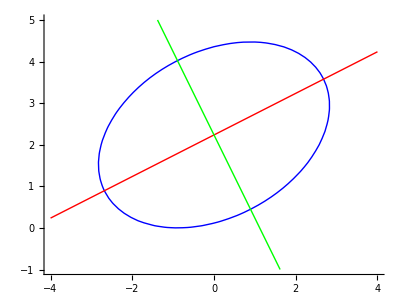

### 解答3.

### 楕円の軸の方程式を求める.

#### 曲線を行列を使って表現する.

```mathematica
A=.
```

```mathematica
A=({{5, -2}, {-2, 8}})
```

{{5,-2},{-2,8}}

```mathematica
Simplify[({{x, y}}).({{5, -2}, {-2, 8}}).({{x}, {y}})+({{20/(√5), -80/(√5)}}).({{x}, {y}})+4]
```

{{4+5 x^2+4 x (√5-y)-16 √5 y+8 y^2}}

#### 行列Aの固有ベクトルを求める.

Eigenvectors[A] は行列Aの固有ベクトルを求める.
Eigenvalues[A]は行列Aの固有値を求める.

```mathematica
Eigenvectors[A]
```

{{-1,2},{2,1}}

```mathematica
Eigenvalues[A]
```

{9,4}

#### 行列Aの固有ベクトルを正規直交化する.

Orthogonalize[v] はベクトルの列 v を正規直交化する.

```mathematica
Orthogonalize[Eigenvectors[A]]
```

{{-1/(√5),2/(√5)},{2/(√5),1/(√5)}}

#### 正規直交化した固有ベクトルを列ベクトルに持つ行列Pを定義する.

```mathematica
P=Transpose[Orthogonalize[Eigenvectors[A]]];
P //MatrixForm
```

(-1/(√5) | 2/(√5)
2/(√5) | 1/(√5))

#### 行列の積 P^t A P を計算してみると対角行列になる.

Transpose[P] は行列Pの転置行列P^t を計算する.

```mathematica
Simplify[Transpose[P].A.P]//MatrixForm
```

(9 | 0
0 | 4)

#### P (a b)を計算し, 曲線の式を簡単にする.

(x
y)=P (a
b) とすると, (x | y)=(a | b)P^t であり,
曲線の方程式は (a | b)P^t A P (a
b)+(20/(√5) | -80/(√5))P(a
b)+4=0 となり
-36 a+9 a^2+4 (-1+b)^2=0 となる.

```mathematica
P.({{a}, {b}})
{{-a/(√5)+(2 b)/(√5)},{(2 a)/(√5)+b/(√5)}}
```

{{-a/(√5)+(2 b)/(√5)},{(2 a)/(√5)+b/(√5)}}

```mathematica
f=5 x^2-4x y + 8 y^2+20/(√5)x-80/(√5)y+4
```

4+4 √5 x+5 x^2-16 √5 y-4 x y+8 y^2

```mathematica
Simplify[f/.{x->-a/(√5)+(2 b)/(√5),y->(2 a)/(√5)+b/(√5)}]
```

-36 a+9 a^2+4 (-1+b)^2

#### 簡単な曲線の式のグラフを描く

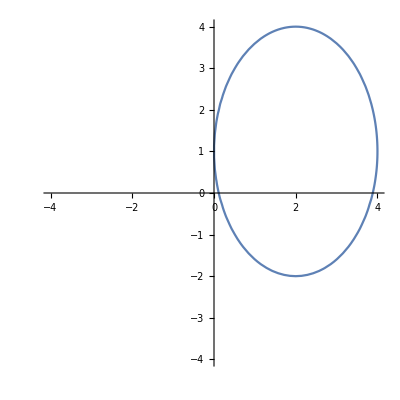

```mathematica
ContourPlot[-36 a+9 a^2+4 (-1+b)^2==0, {a,-4,4},{b,-4,4},Axes->True,Frame->False]
```

平方完成すると、9(a-2)^2+4(b-1)^2-36=0  となり、
ここで(c
d)=(a-2
b-1)と座標変換すると
標準系　c^2/4+d^2/9=1 を得る

```mathematica
Simplify[f/.{x->-(c+2)/(√5)+(2 (d+1))/(√5),y->(2 (c+2))/(√5)+(d+1)/(√5)}]
```

9 c^2+4 (-9+d^2)

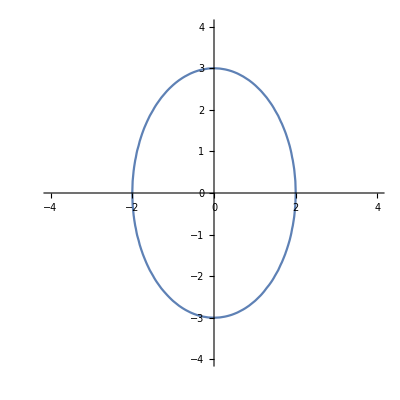

```mathematica
ContourPlot[9 c^2+4 (-9+d^2)==0, {c,-4,4},{d,-4,4},Axes->True,Frame->False]
```

#### 簡単な曲線のグラフでの d軸 (c = 0) の xy平面における式を求める.

```mathematica
Solve[{x==-(c+2)/(√5)+(2 (d+1))/(√5),y==(2 (c+2))/(√5)+(d+1)/(√5),c==0},{y},{c,d}]
```

{{y→1/2 (2 √5+x)}}

#### 簡単な曲線のグラフでの c軸 (d = 0) の xy平面における式を求める.

```mathematica
Solve[{x==-(c+2)/(√5)+(2 (d+1))/(√5),y==(2 (c+2))/(√5)+(d+1)/(√5),d==0},{y},{c,d}]
```

{{y→√5-2 x}}

#### もとの曲線のグラフ中にc軸 (緑) とd軸 (赤) を重ねて描く.

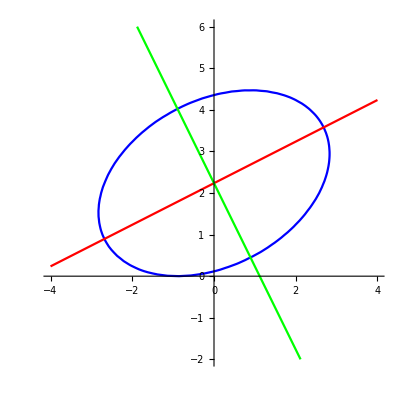

```mathematica
ContourPlot[{5 x^2-4x y+8 y^2+20/(√5)x-80/(√5)y==-4,y==1/2 (2 √5+x),y==√5-2 x}, {x,-4,4},{y,-2,6},Axes->True,Frame->False,ContourStyle->{Blue,Red,Green}]
```

以上から
中心の座標は（0,√5）、軸の直線の式は、y=1/2 (2 √5+x)と　y=√5-2 x